### Exploring Discoverers

```mathematica
(*See GoL-10-Data* for retrieval code*) 
goodData = ;
```

```mathematica
Select[goodData, KeyExistsQ[#, "Discovered by"]&]
```

```mathematica
namesdiscoverers = Select[goodData, KeyExistsQ[#, "Discovered by"] && StringQ[#[["Discovered by"]] ]&][[All, "Discovered by"]];
```

```mathematica
goodData[[1]]
```

<|Pattern type→Spaceship,cells→{},Year of discovery→1989,Discovered by→Dean Hickerson,Period→4,Heat→125.5,Speed→c/4,Wiki→https://conwaylife.com/wiki/119P4H1V0,Name→119P4H1V0|>

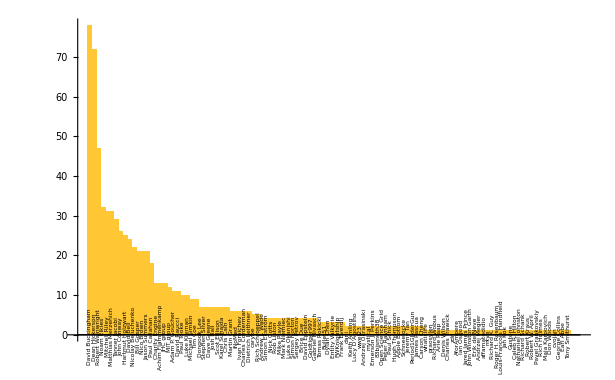

```mathematica
BarChart[ReverseSort[Counts[namesdiscoverers]],ChartLabels->Placed[Keys[ReverseSort[Counts[namesdiscoverers]]],Axis,Style[Rotate[#,Pi/2], 6]&]]
```

```mathematica
Take[Sort[Counts[namesdiscoverers]], -50]
```

<|Nick Gotts→4,Rob Liston→4,Mike Playle→4,Mark Niemiec→4,Luka Okanishi→4,Simon Norton→4,Sergey Petrov→4,Brice Due→4,David Eppstein→4,Goldtiger997→4,Gabriel Nivasch→4,carybe→5,Rich Schroeppel→5,Martin Grant→6,iNoMed→6,Ivan Fomichev→6,Charles Corderman→6,Dietrich Leithner→6,Dongook Lee→7,Stephen Silver→7,Dave Greene→7,Josh Ball→7,Scot Ellison→7,Karel Suhajda→7,Chris Cain→7,Michael Simkin→9,Tim Coe→9,Paul Tooke→10,Luke Kiernan→10,Adam P. Goucher→11,David Raucci→11,MIT group→12,Charity Engine→13,Achim Flammenkamp→13,JHC group→13,Paul Callahan→18,Bill Gosper→21,Nico Brown→21,Jason Summers→21,Nicolay Beluchenko→22,David Bell→24,Hartmut Holzwart→25,John Conway→26,Tanner Jacobi→29,Mitchell Riley→31,Matthias Merzenich→31,Noam Elkies→32,Robert Wainwright→47,Dean Hickerson→72,David Buckingham→78|>

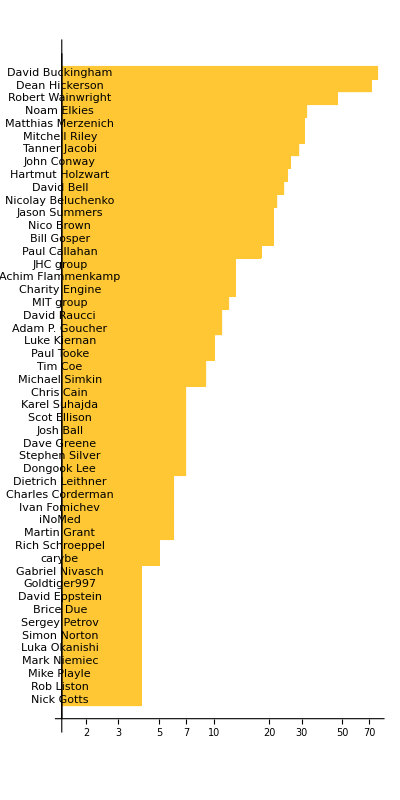

```mathematica
BarChart[Take[Sort[Counts[namesdiscoverers]], -50],ChartLabels->Placed[Keys[Take[Sort[Counts[namesdiscoverers]], -50]],Axis,(*Style[Rotate[#,Pi/2], 6]*)#&], ScalingFunctions->"Log", BarOrigin->Left, PlotRange->100, AspectRatio->2, PlotRangePadding->None]
```

```mathematica
ListLogLogPlot[ReverseSort[Counts[namesdiscoverers]]]
```

-Graphics-

#### With years

```mathematica
w = Values[Values/@Select[goodData, KeyExistsQ[#, "Discovered by"] && StringQ[#[["Discovered by"]] ]&][[All, {"Discovered by", "Year of discovery"}]]];
Catenate[MapIndexed[{#1, First[#2]/.Missing[]-> -Infinity}&, Values[ReverseSortBy[GroupBy[w, First->Last], Length]], {2}]]
```

{{1977,1},{Missing[KeyAbsent,Year of discovery],1},{1977,1},{1972,1},{1973,1},{Missing[KeyAbsent,Year of discovery],1},{1972,1},{Missing[KeyAbsent,Year of discovery],1},{1976,1},{1972,1},{1996,1},{1996,1},{1973,1},{1996,1},{Missing[KeyAbsent,Year of discovery],1},{1973,1},{1972,1},{Missing[KeyAbsent,Year of discovery],1},{1977,1},{Missing[KeyAbsent,Year of discovery],1},{Missing[KeyAbsent,Year of discovery],1},{1972,1},{1980,1},{1976,1},{1996,1},{1977,1},{1977,1},{1972,1},{1996,1},{1996,1},{1996,1},{1996,1},{1972,1},{1978,1},{1990,1},{1991,1},{1978,1},{1996,1},{1996,1},{1972,1},{1972,1},{1973,1},{1973,1},{1992,1},{1983,1},{1980,1},{Missing[KeyAbsent,Year of discovery],1},{1982,1},{1973,1},{1986,1},{Missing[KeyAbsent,Year of discovery],1},{1997,1},{1996,1},{1996,1},{1973,1},{1972,1},{1976,1},{1995,1},{1991,1},{1991,1},{1972,1},{1973,1},{1972,1},{1996,1},{1995,1},{1972,1},{1996,1},{1997,1},{1973,1},{1972,1},{1972,1},{1973,1},{1977,1},{1973,1},{1976,1},{Missing[KeyAbsent,Year of discovery],1},{1977,1},{1972,1},{1989,2},{1991,2},{Missing[KeyAbsent,Year of discovery],2},{1992,2},{1990,2},{1993,2},{1989,2},{1989,2},{1998,2},{1998,2},{1997,2},{1998,2},{1998,2},{1997,2},{1991,2},{1997,2},{1989,2},{1998,2},{1993,2},{1998,2},{1989,2},{1998,2},{1993,2},{1997,2},{1989,2},{1989,2},{2002,2},{1989,2},{2016,2},{1997,2},{1991,2},{1990,2},{1989,2},{1993,2},{1993,2},{1994,2},{2007,2},{1989,2},{1997,2},{1992,2},{1995,2},{1996,2},{2007,2},{1992,2},{1989,2},{1993,2},{1990,2},{1989,2},{1992,2},{1994,2},{1995,2},{1992,2},{1990,2},{1991,2},{1996,2},{Missing[KeyAbsent,Year of discovery],2},{1992,2},{1994,2},{1991,2},{1992,2},{1992,2},{1989,2},{1989,2},{1991,2},{1989,2},{1998,2},{1992,2},{1989,2},{1994,2},{1989,2},{1989,2},{1989,2},{1995,3},{1984,3},{1989,3},{1984,3},{1977,3},{Missing[KeyAbsent,Year of discovery],3},{1972,3},{Missing[KeyAbsent,Year of discovery],3},{1984,3},{1989,3},{1972,3},{1971,3},{Missing[KeyAbsent,Year of discovery],3},{1971,3},{1982,3},{1980,3},{1984,3},{1971,3},{1980,3},{1990,3},{1972,3},{1972,3},{1994,3},{1980,3},{Missing[KeyAbsent,Year of discovery],3},{1979,3},{1989,3},{1984,3},{1985,3},{1971,3},{1990,3},{1972,3},{1984,3},{1978,3},{1989,3},{1971,3},{1985,3},{1971,3},{1989,3},{1982,3},{Missing[KeyAbsent,Year of discovery],3},{1972,3},{1983,3},{1989,3},{1983,3},{Missing[KeyAbsent,Year of discovery],3},{Missing[KeyAbsent,Year of discovery],3},{2002,4},{1994,4},{1995,4},{1997,4},{1995,4},{1997,4},{1997,4},{2002,4},{2002,4},{1994,4},{1997,4},{1995,4},{1995,4},{1997,4},{1995,4},{2010,4},{2010,4},{1994,4},{1999,4},{1994,4},{1996,4},{1998,4},{1998,4},{1997,4},{1998,4},{1999,4},{1998,4},{1996,4},{1995,4},{1998,4},{1994,4},{1994,4},{2022,5},{2022,5},{2023,5},{2023,5},{2022,5},{2022,5},{2023,5},{2022,5},{2023,5},{2022,5},{2022,5},{2023,5},{2023,5},{2023,5},{2022,5},{2024,5},{2022,5},{2023,5},{2022,5},{2022,5},{2023,5},{2023,5},{2023,5},{2022,5},{2023,5},{2022,5},{2022,5},{2022,5},{2022,5},{2023,5},{2006,5},{2013,6},{2010,6},{2017,6},{2015,6},{2015,6},{2017,6},{2017,6},{2010,6},{2014,6},{2010,6},{2016,6},{2014,6},{2009,6},{2012,6},{2010,6},{2012,6},{2014,6},{2011,6},{2010,6},{2011,6},{2010,6},{2018,6},{2011,6},{2023,6},{2012,6},{2012,6},{2017,6},{2011,6},{2010,6},{2025,6},{2009,6},{2016,7},{2020,7},{2015,7},{2015,7},{2018,7},{2015,7},{2017,7},{2017,7},{2017,7},{2022,7},{2015,7},{2014,7},{2016,7},{2016,7},{2017,7},{2017,7},{2015,7},{2016,7},{2018,7},{2016,7},{2016,7},{2016,7},{2022,7},{2016,7},{2017,7},{2022,7},{2015,7},{2017,7},{2017,7},{1970,8},{1970,8},{1970,8},{1969,8},{1969,8},{1970,8},{1970,8},{1969,8},{1969,8},{1969,8},{1970,8},{1970,8},{1970,8},{1970,8},{1970,8},{1970,8},{1969,8},{1969,8},{1970,8},{1970,8},{1970,8},{1970,8},{1970,8},{1969,8},{1970,8},{1969,8},{1994,9},{2004,9},{2004,9},{2004,9},{2004,9},{2005,9},{2009,9},{1992,9},{1992,9},{2004,9},{Missing[KeyAbsent,Year of discovery],9},{Missing[KeyAbsent,Year of discovery],9},{1993,9},{1993,9},{1993,9},{Missing[KeyAbsent,Year of discovery],9},{1992,9},{1992,9},{1992,9},{1993,9},{1992,9},{1992,9},{1993,9},{1993,9},{1992,9},{1992,10},{2005,10},{2005,10},{1992,10},{1992,10},{1993,10},{1992,10},{1992,10},{1992,10},{1992,10},{2005,10},{1996,10},{1971,10},{1998,10},{1992,10},{1992,10},{2010,10},{1992,10},{1993,10},{1993,10},{1993,10},{1997,10},{2005,10},{1998,10},{2009,11},{2010,11},{2005,11},{2005,11},{2009,11},{2009,11},{2009,11},{2009,11},{2006,11},{2010,11},{2009,11},{2009,11},{2009,11},{2004,11},{2005,11},{2009,11},{2003,11},{2005,11},{2009,11},{2004,11},{2005,11},{2005,11},{2023,12},{2023,12},{2022,12},{2022,12},{2022,12},{2023,12},{2023,12},{2023,12},{2015,12},{2023,12},{2022,12},{2023,12},{2022,12},{2023,12},{2023,12},{2023,12},{2022,12},{2022,12},{2022,12},{2023,12},{2022,12},{2000,13},{2002,13},{2002,13},{2007,13},{2004,13},{2000,13},{2005,13},{2005,13},{2001,13},{1999,13},{2000,13},{2000,13},{2005,13},{2000,13},{2004,13},{2009,13},{2005,13},{2000,13},{2006,13},{2012,13},{2000,13},{1994,14},{Missing[KeyAbsent,Year of discovery],14},{1971,14},{Missing[KeyAbsent,Year of discovery],14},{1971,14},{1971,14},{Missing[KeyAbsent,Year of discovery],14},{1970,14},{1971,14},{1994,14},{1994,14},{Missing[KeyAbsent,Year of discovery],14},{1994,14},{1977,14},{1970,14},{1971,14},{1971,14},{1994,14},{1971,14},{1971,14},{1971,14},{1996,15},{1994,15},{1998,15},{1998,15},{1997,15},{1997,15},{1997,15},{1997,15},{1996,15},{1996,15},{1996,15},{1997,15},{1997,15},{1997,15},{1997,15},{1997,15},{1997,15},{1994,15},{1970,16},{1969,16},{1970,16},{1970,16},{1970,16},{1970,16},{1970,16},{1970,16},{1970,16},{1970,16},{1970,16},{1969,16},{1970,16},{2022,17},{2022,17},{2022,17},{2022,17},{2022,17},{2022,17},{2022,17},{2023,17},{2023,17},{2022,17},{2022,17},{2022,17},{2022,17},{1994,18},{1994,18},{1988,18},{1994,18},{1994,18},{1994,18},{1994,18},{1994,18},{1988,18},{1994,18},{1994,18},{1994,18},{1994,18},{1971,19},{1970,19},{1971,19},{1970,19},{1970,19},{1970,19},{1971,19},{1970,19},{1970,19},{1971,19},{1970,19},{1970,19},{2021,20},{2021,20},{2021,20},{2021,20},{2021,20},{2021,20},{2021,20},{2021,20},{2022,20},{2021,20},{2021,20},{2019,21},{2009,21},{2016,21},{2016,21},{2016,21},{2018,21},{2016,21},{2009,21},{2015,21},{2024,21},{2023,21},{2004,22},{2006,22},{2000,22},{2004,22},{2000,22},{2000,22},{2001,22},{2008,22},{2000,22},{2001,22},{2022,23},{2022,23},{2022,23},{2022,23},{2023,23},{2022,23},{2022,23},{2022,23},{2022,23},{2022,23},{1996,24},{1996,24},{1997,24},{1995,24},{1995,24},{1996,24},{1995,24},{2016,24},{1996,24},{2014,25},{2014,25},{2015,25},{2015,25},{2016,25},{2019,25},{2015,25},{2015,25},{2014,25},{2011,26},{2000,26},{1997,26},{1998,26},{2000,26},{1998,26},{1998,26},{2005,27},{2011,27},{2010,27},{2011,27},{2003,27},{2008,27},{2011,27},{2007,28},{2002,28},{2007,28},{2007,28},{2002,28},{2003,28},{2012,28},{2012,29},{2013,29},{2013,29},{2010,29},{2011,29},{2013,29},{2016,29},{2016,30},{2021,30},{2014,30},{2016,30},{2016,30},{2018,30},{2021,30},{2013,31},{2018,31},{2003,31},{2010,31},{2001,31},{2013,31},{2014,31},{2018,32},{2014,32},{2015,32},{2015,32},{2015,32},{2015,32},{2015,32},{2018,33},{2021,33},{2021,33},{2017,33},{2015,33},{2021,33},{2015,34},{2013,34},{2015,34},{2013,34},{2014,34},{2014,34},{2022,35},{2023,35},{2025,35},{2021,35},{2023,35},{2022,35},{1993,36},{1997,36},{1994,36},{1997,36},{1996,36},{1997,36},{Missing[KeyAbsent,Year of discovery],37},{1971,37},{1971,37},{1972,37},{1971,37},{1971,37},{1970,38},{2001,38},{1970,38},{1992,38},{1970,38},{2018,39},{2018,39},{2018,39},{2018,39},{2018,39},{1970,40},{1970,40},{1970,40},{1970,40},{2017,41},{2016,41},{2022,41},{2015,41},{2013,42},{2011,42},{2011,42},{2011,42},{2020,43},{2020,43},{2021,43},{2018,43},{2006,44},{2000,44},{1997,44},{2000,44},{2013,45},{2013,45},{2013,45},{2013,45},{Missing[KeyAbsent,Year of discovery],46},{1973,46},{1972,46},{1995,46},{2016,47},{2017,47},{2016,47},{2023,47},{2020,48},{2021,48},{2022,48},{2023,48},{2002,49},{1999,49},{2001,49},{2001,49},{1998,50},{2001,50},{2000,50},{2000,50},{2006,51},{2006,51},{2006,51},{2006,51},{2020,52},{2020,52},{2010,52},{2019,52},{2005,53},{2018,53},{2005,53},{2023,54},{2024,54},{2025,54},{2022,55},{2022,55},{2025,55},{2019,56},{2019,56},{2022,56},{2021,57},{2020,57},{2020,57},{2017,58},{2015,58},{2018,58},{2022,59},{2020,59},{2010,60},{2010,60},{1972,61},{Missing[KeyAbsent,Year of discovery],61},{2023,62},{2024,62},{Missing[KeyAbsent,Year of discovery],63},{1972,63},{2022,64},{2022,64},{2022,65},{2022,65},{2022,66},{2024,66},{2022,67},{2022,67},{2021,68},{2021,68},{2022,69},{2021,69},{1971,70},{1971,70},{2011,71},{2010,71},{2022,72},{2022,72},{2023,73},{2023,73},{2019,74},{2015,74},{2008,75},{2004,75},{2021,76},{2017,76},{2016,77},{2024,78},{1997,79},{1971,80},{1970,81},{1971,82},{2016,83},{2010,84},{2014,85},{1969,86},{2017,87},{2021,88},{2018,89},{2016,90},{2015,91},{2018,92},{2020,93},{1998,94},{1971,95},{2006,96},{2024,97},{1970,98},{2010,99},{1971,100},{1971,101},{1971,102},{2021,103},{1971,104},{2023,105},{2018,106},{2008,107},{2018,108},{2023,109}}

```mathematica
ListPlot[Catenate[MapIndexed[{#1, First[#2]/.Missing[]-> -Infinity}&, Values[ReverseSortBy[GroupBy[w, First->Last], Length]], {2}]]]
```

-Graphics-

```mathematica
GroupBy[w, (#[["Discovered by"]]&)]
```

<|Dean Hickerson→<|119P4H1V0→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,13-engine Cordership→<|Discovered by→Dean Hickerson,Year of discovery→1991|>,17c/45 reaction→<|Discovered by→Dean Hickerson,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,20P4→<|Discovered by→Dean Hickerson,Year of discovery→1992|>,22P4.3→<|Discovered by→Dean Hickerson,Year of discovery→1990|>,2.3.3→<|Discovered by→Dean Hickerson,Year of discovery→1993|>,24P4.1→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,25P3H1V0.1→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,28P7.1→<|Discovered by→Dean Hickerson,Year of discovery→1998|>,28P7.2→<|Discovered by→Dean Hickerson,Year of discovery→1998|>,29P9→<|Discovered by→Dean Hickerson,Year of discovery→1997|>,37P10.1→<|Discovered by→Dean Hickerson,Year of discovery→1998|>,41P7.2→<|Discovered by→Dean Hickerson,Year of discovery→1998|>,44P14→<|Discovered by→Dean Hickerson,Year of discovery→1997|>,44P5H2V0→<|Discovered by→Dean Hickerson,Year of discovery→1991|>,54P17.1→<|Discovered by→Dean Hickerson,Year of discovery→1997|>,64P2H1V0→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,6-engine Cordership→<|Discovered by→Dean Hickerson,Year of discovery→1998|>,7-engine Cordership→<|Discovered by→Dean Hickerson,Year of discovery→1993|>,7-in-a-row Cordership→<|Discovered by→Dean Hickerson,Year of discovery→1998|>,84P3H1V0.1→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,8-engine Cordership→<|Discovered by→Dean Hickerson,Year of discovery→1998|>,A for all→<|Discovered by→Dean Hickerson,Year of discovery→1993|>,Babbling brook 1→<|Discovered by→Dean Hickerson,Year of discovery→1997|>,Bent keys→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Big glider→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Blom→<|Discovered by→Dean Hickerson,Year of discovery→2002|>,Caterer→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Rattlesnake→<|Discovered by→Dean Hickerson,Year of discovery→2016|>,Champagne glass→<|Discovered by→Dean Hickerson,Year of discovery→1997|>,Cord puller→<|Discovered by→Dean Hickerson,Year of discovery→1991|>,Crystallization and decay oscillator→<|Discovered by→Dean Hickerson,Year of discovery→1990|>,Double caterer→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Electric fence→<|Discovered by→Dean Hickerson,Year of discovery→1993|>,Enterprise→<|Discovered by→Dean Hickerson,Year of discovery→1993|>,Fountain→<|Discovered by→Dean Hickerson,Year of discovery→1994|>,Four eaters→<|Discovered by→Dean Hickerson,Year of discovery→2007|>,Fumarole→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Grin reagent→<|Discovered by→Dean Hickerson,Year of discovery→1997|>,Hacksaw→<|Discovered by→Dean Hickerson,Year of discovery→1992|>,Heavyweight volcano→<|Discovered by→Dean Hickerson,Year of discovery→1995|>,Herschel stopper→<|Discovered by→Dean Hickerson,Year of discovery→1996|>,Land of lakes→<|Discovered by→Dean Hickerson,Year of discovery→2007|>,Middleweight volcano→<|Discovered by→Dean Hickerson,Year of discovery→1992|>,Monogram→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Muttering moat 1→<|Discovered by→Dean Hickerson,Year of discovery→1993|>,New five→<|Discovered by→Dean Hickerson,Year of discovery→1990|>,Odd keys→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,p120-based PRNG→<|Discovered by→Dean Hickerson,Year of discovery→1992|>,p124 lumps of muck hassler→<|Discovered by→Dean Hickerson,Year of discovery→1994|>,p35 beehive hassler→<|Discovered by→Dean Hickerson,Year of discovery→1995|>,p50 glider shuttle→<|Discovered by→Dean Hickerson,Year of discovery→1992|>,P94S→<|Discovered by→Dean Hickerson,Year of discovery→1990|>,Parabolic sawtooth→<|Discovered by→Dean Hickerson,Year of discovery→1991|>,Period-50 glider gun→<|Discovered by→Dean Hickerson,Year of discovery→1996|>,Period-90 glider gun→<|Discovered by→Dean Hickerson,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Ring of fire→<|Discovered by→Dean Hickerson,Year of discovery→1992|>,Rumbling river 1→<|Discovered by→Dean Hickerson,Year of discovery→1994|>,Sawtooth 1212→<|Discovered by→Dean Hickerson,Year of discovery→1991|>,Sawtooth 1846→<|Discovered by→Dean Hickerson,Year of discovery→1992|>,Sawtooth 633→<|Discovered by→Dean Hickerson,Year of discovery→1992|>,Short keys→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Statorless p6→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Switchwave→<|Discovered by→Dean Hickerson,Year of discovery→1991|>,Tempest→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Thumb 1→<|Discovered by→Dean Hickerson,Year of discovery→1998|>,Toaster→<|Discovered by→Dean Hickerson,Year of discovery→1992|>,Triple caterer→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Trivial p6-1→<|Discovered by→Dean Hickerson,Year of discovery→1994|>,Turning toads→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Turtle→<|Discovered by→Dean Hickerson,Year of discovery→1989|>,Windmill→<|Discovered by→Dean Hickerson,Year of discovery→1989|>|>,Mitchell Riley→<|120P34→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,42P14→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,42P38→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,44P49→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,62P83→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,70P26→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,72P119→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,74P34→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,86P107→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,92P23→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,92P59→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,94P53→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,Cribbage→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,G-to-pi catalyst (August 2023)→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,HRx65R→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,Lx65 duplicator→<|Discovered by→Mitchell Riley,Year of discovery→2024|>,p111 R-pentomino hassler→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,p13 domino sparker→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,p16-assisted period-32 glider gun→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,p171 pi-heptomino hassler→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,p26 honey farm hassler→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,p47 lumps of muck hassler→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,p59 pi-heptomino hassler→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,p75 I-heptomino hassler→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,p82 lumps of muck hassler→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,p84 honey farm hassler→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,p94 R-pentomino hassler→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,Period-113 glider gun→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,Period-25 glider gun→<|Discovered by→Mitchell Riley,Year of discovery→2022|>,Period-61 glider gun (2023)→<|Discovered by→Mitchell Riley,Year of discovery→2023|>,Riley's breeder→<|Discovered by→Mitchell Riley,Year of discovery→2006|>|>,Noam Elkies→<|123P27.1→<|Discovered by→Noam Elkies,Year of discovery→2002|>,134P25→<|Discovered by→Noam Elkies,Year of discovery→1994|>,145P20→<|Discovered by→Noam Elkies,Year of discovery→1995|>,168P22.1→<|Discovered by→Noam Elkies,Year of discovery→1997|>,22P36→<|Discovered by→Noam Elkies,Year of discovery→1995|>,258P3→<|Discovered by→Noam Elkies,Year of discovery→1997|>,258P3 on Achim's p11→<|Discovered by→Noam Elkies,Year of discovery→1997|>,69P48→<|Discovered by→Noam Elkies,Year of discovery→2002|>,98P25→<|Discovered by→Noam Elkies,Year of discovery→2002|>,Crown→<|Discovered by→Noam Elkies,Year of discovery→1994|>,Elkies' p5→<|Discovered by→Noam Elkies,Year of discovery→1997|>,Four molds hassling eight blocks→<|Discovered by→Noam Elkies,Year of discovery→1995|>,p156 Hans Leo hassler→<|Discovered by→Noam Elkies,Year of discovery→1995|>,p15 pre-pulsar spaceship→<|Discovered by→Noam Elkies,Year of discovery→1997|>,p18 bi-block hassler→<|Discovered by→Noam Elkies,Year of discovery→1995|>,p32 blinker hassler→<|Discovered by→Noam Elkies,Year of discovery→2010|>,p32 blinker hassler 2→<|Discovered by→Noam Elkies,Year of discovery→2010|>,p42 glider shuttle→<|Discovered by→Noam Elkies,Year of discovery→1994|>,p49 bouncer loop→<|Discovered by→Noam Elkies,Year of discovery→1999|>,p50 traffic jam→<|Discovered by→Noam Elkies,Year of discovery→1994|>,p52 R-pentomino hassler→<|Discovered by→Noam Elkies,Year of discovery→1996|>,p5 bouncer→<|Discovered by→Noam Elkies,Year of discovery→1998|>,p6 bouncer→<|Discovered by→Noam Elkies,Year of discovery→1998|>,p6 pipsquirter→<|Discovered by→Noam Elkies,Year of discovery→1997|>,p7 bouncer→<|Discovered by→Noam Elkies,Year of discovery→1998|>,p7 pipsquirter→<|Discovered by→Noam Elkies,Year of discovery→1999|>,p8 bouncer→<|Discovered by→Noam Elkies,Year of discovery→1998|>,Period-690 glider gun→<|Discovered by→Noam Elkies,Year of discovery→1996|>,Pi orbital→<|Discovered by→Noam Elkies,Year of discovery→1995|>,Superfountain→<|Discovered by→Noam Elkies,Year of discovery→1998|>,Traffic circle→<|Discovered by→Noam Elkies,Year of discovery→1994|>,Twin bees shuttles hassling blinker→<|Discovered by→Noam Elkies,Year of discovery→1994|>|>,Robert Wainwright→<|124P21→<|Discovered by→Robert Wainwright,Year of discovery→1995|>,6 bits→<|Discovered by→Robert Wainwright,Year of discovery→1984|>,Baker's dozen→<|Discovered by→Robert Wainwright,Year of discovery→1989|>,Blinker puffer 1→<|Discovered by→Robert Wainwright,Year of discovery→1984|>,Blinkers bit pole→<|Discovered by→Robert Wainwright,Year of discovery→1977|>,Blocker→<|Discovered by→Robert Wainwright,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Block on griddle→<|Discovered by→Robert Wainwright,Year of discovery→1972|>,By flops→<|Discovered by→Robert Wainwright,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Carnival shuttle→<|Discovered by→Robert Wainwright,Year of discovery→1984|>,Cross→<|Discovered by→Robert Wainwright,Year of discovery→1989|>,Dinner table→<|Discovered by→Robert Wainwright,Year of discovery→1972|>,Double ewe→<|Discovered by→Robert Wainwright,Year of discovery→1971|>,Double X→<|Discovered by→Robert Wainwright,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,French kiss→<|Discovered by→Robert Wainwright,Year of discovery→1971|>,Heart→<|Discovered by→Robert Wainwright,Year of discovery→1982|>,Heavyweight emulator→<|Discovered by→Robert Wainwright,Year of discovery→1980|>,Hectic→<|Discovered by→Robert Wainwright,Year of discovery→1984|>,Hustler→<|Discovered by→Robert Wainwright,Year of discovery→1971|>,Lightweight emulator→<|Discovered by→Robert Wainwright,Year of discovery→1980|>,Loaflipflop→<|Discovered by→Robert Wainwright,Year of discovery→1990|>,Long hook with tail→<|Discovered by→Robert Wainwright,Year of discovery→1972|>,Long shillelagh→<|Discovered by→Robert Wainwright,Year of discovery→1972|>,Metamorphosis II→<|Discovered by→Robert Wainwright,Year of discovery→1994|>,Middleweight emulator→<|Discovered by→Robert Wainwright,Year of discovery→1980|>,Mini pressure cooker→<|Discovered by→Robert Wainwright,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Octagon 4→<|Discovered by→Robert Wainwright,Year of discovery→1979|>,p165 glider shuttle→<|Discovered by→Robert Wainwright,Year of discovery→1989|>,p36 toad hassler→<|Discovered by→Robert Wainwright,Year of discovery→1984|>,Pulshuttle V→<|Discovered by→Robert Wainwright,Year of discovery→1985|>,Quasar→<|Discovered by→Robert Wainwright,Year of discovery→1971|>,Two blockers hassling R-pentomino→<|Discovered by→Robert Wainwright,Year of discovery→1990|>,Roteightor→<|Discovered by→Robert Wainwright,Year of discovery→1972|>,Sailboat→<|Discovered by→Robert Wainwright,Year of discovery→1984|>,Sixty-nine→<|Discovered by→Robert Wainwright,Year of discovery→1978|>,Skewed traffic light→<|Discovered by→Robert Wainwright,Year of discovery→1989|>,Spiral→<|Discovered by→Robert Wainwright,Year of discovery→1971|>,Stillater→<|Discovered by→Robert Wainwright,Year of discovery→1985|>,Titanic toroidal traveler→<|Discovered by→Robert Wainwright,Year of discovery→1971|>,T-nosed p4→<|Discovered by→Robert Wainwright,Year of discovery→1989|>,Trice tongs→<|Discovered by→Robert Wainwright,Year of discovery→1982|>,Tubber→<|Discovered by→Robert Wainwright,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Tub with long tail→<|Discovered by→Robert Wainwright,Year of discovery→1972|>,Tumbling T-tetson→<|Discovered by→Robert Wainwright,Year of discovery→1983|>,Twirling T-tetsons 2→<|Discovered by→Robert Wainwright,Year of discovery→1989|>,Two pre-L hasslers→<|Discovered by→Robert Wainwright,Year of discovery→1983|>,Wainwright's tagalong→<|Discovered by→Robert Wainwright,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Washing machine→<|Discovered by→Robert Wainwright,Year of discovery→Missing[KeyAbsent,Year of discovery]|>|>,Nicolay Beluchenko→<|128P10.2→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,56P27→<|Discovered by→Nicolay Beluchenko,Year of discovery→2010|>,33P4H1V1→<|Discovered by→Nicolay Beluchenko,Year of discovery→2005|>,37P4H1V1.1→<|Discovered by→Nicolay Beluchenko,Year of discovery→2005|>,38P7.2→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,46P10→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,48P22.1→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,Beluchenko's p13→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,67P5H1V1→<|Discovered by→Nicolay Beluchenko,Year of discovery→2006|>,Beluchenko's other p37→<|Discovered by→Nicolay Beluchenko,Year of discovery→2010|>,Beluchenko's p37→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,Beluchenko's p40→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,Beluchenko's p51→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,Blonker→<|Discovered by→Nicolay Beluchenko,Year of discovery→2004|>,Crane→<|Discovered by→Nicolay Beluchenko,Year of discovery→2005|>,Eye of Sauron→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,Fire-spitting→<|Discovered by→Nicolay Beluchenko,Year of discovery→2003|>,One per generation→<|Discovered by→Nicolay Beluchenko,Year of discovery→2005|>,p11 pinwheel→<|Discovered by→Nicolay Beluchenko,Year of discovery→2009|>,p6 shuttle→<|Discovered by→Nicolay Beluchenko,Year of discovery→2004|>,Seal→<|Discovered by→Nicolay Beluchenko,Year of discovery→2005|>,T-nosed p5→<|Discovered by→Nicolay Beluchenko,Year of discovery→2005|>|>,Dongook Lee→<|132P7→<|Discovered by→Dongook Lee,Year of discovery→2016|>,62P7→<|Discovered by→Dongook Lee,Year of discovery→2021|>,c/12 R-pentomino crawler→<|Discovered by→Dongook Lee,Year of discovery→2014|>,p21 honey farm hassler→<|Discovered by→Dongook Lee,Year of discovery→2016|>,p35 honey farm hassler→<|Discovered by→Dongook Lee,Year of discovery→2016|>,p5 pipsquirter→<|Discovered by→Dongook Lee,Year of discovery→2018|>,Strictly volatile p4→<|Discovered by→Dongook Lee,Year of discovery→2021|>|>,whatislife→<|135-degree LWSS-to-G→<|Discovered by→whatislife,Year of discovery→2024|>|>,Matthias Merzenich→<|135-degree MWSS-to-G→<|Discovered by→Matthias Merzenich,Year of discovery→2013|>,24P10→<|Discovered by→Matthias Merzenich,Year of discovery→2010|>,339P7H1V0→<|Discovered by→Matthias Merzenich,Year of discovery→2017|>,34P5H2V0→<|Discovered by→Matthias Merzenich,Year of discovery→2015|>,35P12.1→<|Discovered by→Matthias Merzenich,Year of discovery→2015|>,40P4H1V0.1→<|Discovered by→Matthias Merzenich,Year of discovery→2017|>,40P4H1V0.2→<|Discovered by→Matthias Merzenich,Year of discovery→2017|>,44P10→<|Discovered by→Matthias Merzenich,Year of discovery→2010|>,50P9→<|Discovered by→Matthias Merzenich,Year of discovery→2014|>,58P5H1V1→<|Discovered by→Matthias Merzenich,Year of discovery→2010|>,600P6H1V0→<|Discovered by→Matthias Merzenich,Year of discovery→2016|>,65P48→<|Discovered by→Matthias Merzenich,Year of discovery→2014|>,68P32→<|Discovered by→Matthias Merzenich,Year of discovery→2009|>,86P6H3V0→<|Discovered by→Matthias Merzenich,Year of discovery→2012|>,Merzenich's p31→<|Discovered by→Matthias Merzenich,Year of discovery→2010|>,HLx111R→<|Discovered by→Matthias Merzenich,Year of discovery→2012|>,Honey thieves→<|Discovered by→Matthias Merzenich,Year of discovery→2014|>,Lobster→<|Discovered by→Matthias Merzenich,Year of discovery→2011|>,Merzenich's p11→<|Discovered by→Matthias Merzenich,Year of discovery→2010|>,Merzenich's p18→<|Discovered by→Matthias Merzenich,Year of discovery→2011|>,Merzenich's p64→<|Discovered by→Matthias Merzenich,Year of discovery→2010|>,MWSS behind Coe ship→<|Discovered by→Matthias Merzenich,Year of discovery→2018|>,p11 double-length signal injector→<|Discovered by→Matthias Merzenich,Year of discovery→2011|>,p24 gliderless LWSS gun→<|Discovered by→Matthias Merzenich,Year of discovery→2023|>,p26 dependent reflector loop→<|Discovered by→Matthias Merzenich,Year of discovery→2012|>,p31 dependent reflector loop→<|Discovered by→Matthias Merzenich,Year of discovery→2012|>,p46 gliderless MWSS gun→<|Discovered by→Matthias Merzenich,Year of discovery→2017|>,p48 pi-heptomino hassler→<|Discovered by→Matthias Merzenich,Year of discovery→2011|>,Period-45 glider gun→<|Discovered by→Matthias Merzenich,Year of discovery→2010|>,Period-57 glider gun→<|Discovered by→Matthias Merzenich,Year of discovery→2025|>,Period-88 glider gun→<|Discovered by→Matthias Merzenich,Year of discovery→2009|>|>,Paul Tooke→<|160P10H2V0→<|Discovered by→Paul Tooke,Year of discovery→2004|>,274P6H1V0→<|Discovered by→Paul Tooke,Year of discovery→2006|>,30P5H2V0→<|Discovered by→Paul Tooke,Year of discovery→2000|>,3-engine Cordership→<|Discovered by→Paul Tooke,Year of discovery→2004|>,51P5H2V0.1→<|Discovered by→Paul Tooke,Year of discovery→2000|>,51P5H2V0.2→<|Discovered by→Paul Tooke,Year of discovery→2000|>,55P9H3V0→<|Discovered by→Paul Tooke,Year of discovery→2001|>,Bulldozer→<|Discovered by→Paul Tooke,Year of discovery→2008|>,Dragon→<|Discovered by→Paul Tooke,Year of discovery→2000|>,Frothing puffer→<|Discovered by→Paul Tooke,Year of discovery→2001|>|>,Bill Gosper→<|186P24→<|Discovered by→Bill Gosper,Year of discovery→1994|>,Bi-gun→<|Discovered by→Bill Gosper,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Breeder 1→<|Discovered by→Bill Gosper,Year of discovery→1971|>,Centinal→<|Discovered by→Bill Gosper,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Eater 1→<|Discovered by→Bill Gosper,Year of discovery→1971|>,Ecologist→<|Discovered by→Bill Gosper,Year of discovery→1971|>,Glider train→<|Discovered by→Bill Gosper,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Gosper glider gun→<|Discovered by→Bill Gosper,Year of discovery→1970|>,New gun 1→<|Discovered by→Bill Gosper,Year of discovery→1971|>,p110 traffic jam→<|Discovered by→Bill Gosper,Year of discovery→1994|>,p200 traffic jam→<|Discovered by→Bill Gosper,Year of discovery→1994|>,p29 pentadecathlon hassler→<|Discovered by→Bill Gosper,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,p48 toad hassler→<|Discovered by→Bill Gosper,Year of discovery→1994|>,Pentoad→<|Discovered by→Bill Gosper,Year of discovery→1977|>,Period-60 glider gun→<|Discovered by→Bill Gosper,Year of discovery→1970|>,Puffer 1→<|Discovered by→Bill Gosper,Year of discovery→1971|>,Puffer 2→<|Discovered by→Bill Gosper,Year of discovery→1971|>,Ship in a bottle→<|Discovered by→Bill Gosper,Year of discovery→1994|>,Twin bees shuttle→<|Discovered by→Bill Gosper,Year of discovery→1971|>,Twin bees shuttle spark→<|Discovered by→Bill Gosper,Year of discovery→1971|>,Two eaters→<|Discovered by→Bill Gosper,Year of discovery→1971|>|>,Andrew J. Wade→<|186P7H2V0→<|Discovered by→Andrew J. Wade,Year of discovery→2020|>,409P6H1V0→<|Discovered by→Andrew J. Wade,Year of discovery→2020|>,Gemini→<|Discovered by→Andrew J. Wade,Year of discovery→2010|>,Scholar→<|Discovered by→Andrew J. Wade,Year of discovery→2019|>|>,Stephen Silver→<|1×N quadratic growth→<|Discovered by→Stephen Silver,Year of discovery→2011|>,Edge-repair spaceship 2→<|Discovered by→Stephen Silver,Year of discovery→2000|>,RF48H→<|Discovered by→Stephen Silver,Year of discovery→1997|>,RNE-19T84→<|Discovered by→Stephen Silver,Year of discovery→1998|>,Silver's p5→<|Discovered by→Stephen Silver,Year of discovery→2000|>,Silver's reflector→<|Discovered by→Stephen Silver,Year of discovery→1998|>,Silver G-to-H→<|Discovered by→Stephen Silver,Year of discovery→1998|>|>,Nico Brown→<|204P41→<|Discovered by→Nico Brown,Year of discovery→2023|>,246P41→<|Discovered by→Nico Brown,Year of discovery→2023|>,54P94→<|Discovered by→Nico Brown,Year of discovery→2022|>,70P23→<|Discovered by→Nico Brown,Year of discovery→2022|>,Diamondback→<|Discovered by→Nico Brown,Year of discovery→2022|>,Odd traffic stop→<|Discovered by→Nico Brown,Year of discovery→2023|>,p16 century shuttle→<|Discovered by→Nico Brown,Year of discovery→2023|>,p17 R-pentomino hassler→<|Discovered by→Nico Brown,Year of discovery→2023|>,p18 honey farm hassler→<|Discovered by→Nico Brown,Year of discovery→2015|>,p41 pi-heptomino hassler→<|Discovered by→Nico Brown,Year of discovery→2023|>,p43 pi-heptomino hassler→<|Discovered by→Nico Brown,Year of discovery→2022|>,p49 pi-heptomino hassler→<|Discovered by→Nico Brown,Year of discovery→2023|>,p59 dependent reflector loop→<|Discovered by→Nico Brown,Year of discovery→2022|>,p67 B-heptomino hassler→<|Discovered by→Nico Brown,Year of discovery→2023|>,p68 century hassler→<|Discovered by→Nico Brown,Year of discovery→2023|>,p71 dependent reflector loop→<|Discovered by→Nico Brown,Year of discovery→2023|>,p86 R-pentomino hassler→<|Discovered by→Nico Brown,Year of discovery→2022|>,Period-34 glider gun→<|Discovered by→Nico Brown,Year of discovery→2022|>,Period-43 glider gun→<|Discovered by→Nico Brown,Year of discovery→2022|>,Period-49 glider gun (April 2023)→<|Discovered by→Nico Brown,Year of discovery→2023|>,Period-51 glider gun→<|Discovered by→Nico Brown,Year of discovery→2022|>|>,Martin Grant→<|209P8→<|Discovered by→Martin Grant,Year of discovery→2018|>,HNE16T14→<|Discovered by→Martin Grant,Year of discovery→2021|>,p11 domino sparker→<|Discovered by→Martin Grant,Year of discovery→2021|>,Period-92 glider gun→<|Discovered by→Martin Grant,Year of discovery→2017|>,Rx262→<|Discovered by→Martin Grant,Year of discovery→2015|>,T-nosed p7→<|Discovered by→Martin Grant,Year of discovery→2021|>|>,dani→<|20-cell quadratic growth→<|Discovered by→dani,Year of discovery→2022|>,21-cell quadratic growth→<|Discovered by→dani,Year of discovery→2022|>|>,Keith Amling→<|232P7H3V0→<|Discovered by→Keith Amling,Year of discovery→2022|>,Quartermax→<|Discovered by→Keith Amling,Year of discovery→2022|>|>,Tomas Rokicki→<|23334M→<|Discovered by→Tomas Rokicki,Year of discovery→2005|>,54P3H1V0→<|Discovered by→Tomas Rokicki,Year of discovery→2018|>,7468M→<|Discovered by→Tomas Rokicki,Year of discovery→2005|>|>,Hartmut Holzwart→<|233P3H1V0→<|Discovered by→Hartmut Holzwart,Year of discovery→1994|>,35P4H1V1→<|Discovered by→Hartmut Holzwart,Year of discovery→2004|>,37P4H1V1.2→<|Discovered by→Hartmut Holzwart,Year of discovery→2004|>,38P4H1V1.1→<|Discovered by→Hartmut Holzwart,Year of discovery→2004|>,38P4H1V1.2→<|Discovered by→Hartmut Holzwart,Year of discovery→2004|>,39P4H1V1→<|Discovered by→Hartmut Holzwart,Year of discovery→2005|>,56P6H1V0→<|Discovered by→Hartmut Holzwart,Year of discovery→2009|>,70P2H1V0.1→<|Discovered by→Hartmut Holzwart,Year of discovery→1992|>,70P5H2V0→<|Discovered by→Hartmut Holzwart,Year of discovery→1992|>,B29→<|Discovered by→Hartmut Holzwart,Year of discovery→2004|>,Barge 2 (spaceship)→<|Discovered by→Hartmut Holzwart,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Big A→<|Discovered by→Hartmut Holzwart,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Boatstretcher 1→<|Discovered by→Hartmut Holzwart,Year of discovery→1993|>,Bracket pulsar→<|Discovered by→Hartmut Holzwart,Year of discovery→1993|>,Cross 2→<|Discovered by→Hartmut Holzwart,Year of discovery→1993|>,Hammerhead→<|Discovered by→Hartmut Holzwart,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Hivenudger→<|Discovered by→Hartmut Holzwart,Year of discovery→1992|>,Hivenudger 2→<|Discovered by→Hartmut Holzwart,Year of discovery→1992|>,Non-monotonic spaceship 1→<|Discovered by→Hartmut Holzwart,Year of discovery→1992|>,Orion→<|Discovered by→Hartmut Holzwart,Year of discovery→1993|>,Sidecar→<|Discovered by→Hartmut Holzwart,Year of discovery→1992|>,Sparky→<|Discovered by→Hartmut Holzwart,Year of discovery→1992|>,Star→<|Discovered by→Hartmut Holzwart,Year of discovery→1993|>,Wing (spaceship)→<|Discovered by→Hartmut Holzwart,Year of discovery→1993|>,x66→<|Discovered by→Hartmut Holzwart,Year of discovery→1992|>|>,Simon Ekström→<|24827M→<|Discovered by→Simon Ekström,Year of discovery→2017|>,Fireship→<|Discovered by→Simon Ekström,Year of discovery→2016|>,NW-2T16→<|Discovered by→Simon Ekström,Year of discovery→2022|>,SW1T43→<|Discovered by→Simon Ekström,Year of discovery→2015|>|>,Michael Simkin→<|24-cell quadratic growth→<|Discovered by→Michael Simkin,Year of discovery→2014|>,25-cell quadratic growth→<|Discovered by→Michael Simkin,Year of discovery→2014|>,B60→<|Discovered by→Michael Simkin,Year of discovery→2015|>,BRx46B→<|Discovered by→Michael Simkin,Year of discovery→2015|>,Caterloopillar→<|Discovered by→Michael Simkin,Year of discovery→2016|>,Remini→<|Discovered by→Michael Simkin,Year of discovery→2019|>,Simkin's p60→<|Discovered by→Michael Simkin,Year of discovery→2015|>,Simkin glider gun→<|Discovered by→Michael Simkin,Year of discovery→2015|>,Switch engine ping-pong→<|Discovered by→Michael Simkin,Year of discovery→2014|>|>,Charity Engine→<|30P25→<|Discovered by→Charity Engine,Year of discovery→2022|>,32P21→<|Discovered by→Charity Engine,Year of discovery→2022|>,34P20→<|Discovered by→Charity Engine,Year of discovery→2022|>,34P7→<|Discovered by→Charity Engine,Year of discovery→2022|>,54P12H6V0→<|Discovered by→Charity Engine,Year of discovery→2022|>,58P8H4V0→<|Discovered by→Charity Engine,Year of discovery→2022|>,Charity's p16→<|Discovered by→Charity Engine,Year of discovery→2022|>,Charity's p25→<|Discovered by→Charity Engine,Year of discovery→2023|>,Charity's p30→<|Discovered by→Charity Engine,Year of discovery→2023|>,Meatball→<|Discovered by→Charity Engine,Year of discovery→2022|>,p11 thumb→<|Discovered by→Charity Engine,Year of discovery→2022|>,p28 block puffer→<|Discovered by→Charity Engine,Year of discovery→2022|>,P6 domino fountain→<|Discovered by→Charity Engine,Year of discovery→2022|>|>,Lucy D'Agostino→<|255P132→<|Discovered by→Lucy D'Agostino,Year of discovery→2022|>,L141→<|Discovered by→Lucy D'Agostino,Year of discovery→2024|>|>,David Bell→<|25P3H1V0.2→<|Discovered by→David Bell,Year of discovery→1992|>,4-engine Cordership→<|Discovered by→David Bell,Year of discovery→2005|>,5-engine Cordership→<|Discovered by→David Bell,Year of discovery→2005|>,60P3H1V0.3→<|Discovered by→David Bell,Year of discovery→1992|>,Blinker puffer 2→<|Discovered by→David Bell,Year of discovery→1992|>,Bracket quasar→<|Discovered by→David Bell,Year of discovery→1993|>,Brain→<|Discovered by→David Bell,Year of discovery→1992|>,Dart→<|Discovered by→David Bell,Year of discovery→1992|>,Edge-repair spaceship 1→<|Discovered by→David Bell,Year of discovery→1992|>,Fly→<|Discovered by→David Bell,Year of discovery→1992|>,Moving sawtooth→<|Discovered by→David Bell,Year of discovery→2005|>,p5760 unit Life cell→<|Discovered by→David Bell,Year of discovery→1996|>,Pi ship 1→<|Discovered by→David Bell,Year of discovery→1971|>,Pre-pulsar spaceship→<|Discovered by→David Bell,Year of discovery→1998|>,Pushalong 1→<|Discovered by→David Bell,Year of discovery→1992|>,Sawtooth 1163→<|Discovered by→David Bell,Year of discovery→1992|>,Sawtooth 260→<|Discovered by→David Bell,Year of discovery→2010|>,Sawtooth 362→<|Discovered by→David Bell,Year of discovery→1992|>,Slow puffer 1→<|Discovered by→David Bell,Year of discovery→1993|>,Slow puffer 2→<|Discovered by→David Bell,Year of discovery→1993|>,Spacefiller 1→<|Discovered by→David Bell,Year of discovery→1993|>,Spider→<|Discovered by→David Bell,Year of discovery→1997|>,Switch engine channel→<|Discovered by→David Bell,Year of discovery→2005|>,Wasp→<|Discovered by→David Bell,Year of discovery→1998|>|>,Nick Gotts→<|26-cell quadratic growth→<|Discovered by→Nick Gotts,Year of discovery→2006|>,Catacryst→<|Discovered by→Nick Gotts,Year of discovery→2000|>,Jaws→<|Discovered by→Nick Gotts,Year of discovery→1997|>,Metacatacryst→<|Discovered by→Nick Gotts,Year of discovery→2000|>|>,Bullet51→<|28P7.3→<|Discovered by→Bullet51,Year of discovery→2017|>,53P13→<|Discovered by→Bullet51,Year of discovery→2015|>,55P10→<|Discovered by→Bullet51,Year of discovery→2018|>|>,Jason Summers→<|295P5H1V1→<|Discovered by→Jason Summers,Year of discovery→2000|>,31P8H4V0→<|Discovered by→Jason Summers,Year of discovery→2002|>,50P35→<|Discovered by→Jason Summers,Year of discovery→2002|>,52P84→<|Discovered by→Jason Summers,Year of discovery→2007|>,Period-156 glider gun→<|Discovered by→Jason Summers,Year of discovery→2004|>,72P6H2V0→<|Discovered by→Jason Summers,Year of discovery→2000|>,86P5H1V1→<|Discovered by→Jason Summers,Year of discovery→2005|>,94P27.1→<|Discovered by→Jason Summers,Year of discovery→2005|>,Backrake 1→<|Discovered by→Jason Summers,Year of discovery→2001|>,Canada goose→<|Discovered by→Jason Summers,Year of discovery→1999|>,Jason's p22→<|Discovered by→Jason Summers,Year of discovery→2000|>,Crab→<|Discovered by→Jason Summers,Year of discovery→2000|>,Halfmax→<|Discovered by→Jason Summers,Year of discovery→2005|>,Jason's p33→<|Discovered by→Jason Summers,Year of discovery→2000|>,Jason's p36→<|Discovered by→Jason Summers,Year of discovery→2004|>,Maximum volatility gun→<|Discovered by→Jason Summers,Year of discovery→2009|>,p72 quasi-shuttle→<|Discovered by→Jason Summers,Year of discovery→2005|>,p8 swan tagalong→<|Discovered by→Jason Summers,Year of discovery→2000|>,Sidewinder→<|Discovered by→Jason Summers,Year of discovery→2006|>,Statorless p3→<|Discovered by→Jason Summers,Year of discovery→2012|>,Wings→<|Discovered by→Jason Summers,Year of discovery→2000|>|>,praosylen→<|2-engine Cordership→<|Discovered by→praosylen,Year of discovery→2017|>|>,iNoMed→<|30P3→<|Discovered by→iNoMed,Year of discovery→2022|>,32P21 phase-shifting p5→<|Discovered by→iNoMed,Year of discovery→2023|>,p80 gliderless HWSS gun→<|Discovered by→iNoMed,Year of discovery→2025|>,Period-144 glider gun→<|Discovered by→iNoMed,Year of discovery→2021|>,Period-41 glider gun→<|Discovered by→iNoMed,Year of discovery→2023|>,Twin bees shuttle on 21P4.1→<|Discovered by→iNoMed,Year of discovery→2022|>|>,Rob Liston→<|Rob's p16→<|Discovered by→Rob Liston,Year of discovery→2020|>,49768M→<|Discovered by→Rob Liston,Year of discovery→2020|>,50093M→<|Discovered by→Rob Liston,Year of discovery→2021|>,Wilma→<|Discovered by→Rob Liston,Year of discovery→2018|>|>,Mike Playle→<|31.4→<|Discovered by→Mike Playle,Year of discovery→2013|>,AK-94→<|Discovered by→Mike Playle,Year of discovery→2013|>,p43 Snark loop→<|Discovered by→Mike Playle,Year of discovery→2013|>,p67 Snark loop→<|Discovered by→Mike Playle,Year of discovery→2013|>|>,Dave Greene→<|31c/240 Herschel-pair climber→<|Discovered by→Dave Greene,Year of discovery→2013|>,42100M→<|Discovered by→Dave Greene,Year of discovery→2018|>,6-engine Cordership gun→<|Discovered by→Dave Greene,Year of discovery→2003|>,6-in-a-row Cordership→<|Discovered by→Dave Greene,Year of discovery→2010|>,Boojum reflector→<|Discovered by→Dave Greene,Year of discovery→2001|>,Linear propagator→<|Discovered by→Dave Greene,Year of discovery→2013|>,Shield bug→<|Discovered by→Dave Greene,Year of discovery→2014|>|>,Richard Wobus→<|32829M→<|Discovered by→Richard Wobus,Year of discovery→2010|>|>,wwei23→<|32P4H2V0→<|Discovered by→wwei23,Year of discovery→2022|>,4-in-a-row Cordership→<|Discovered by→wwei23,Year of discovery→2020|>|>,Arie Paap→<|33P3.1→<|Discovered by→Arie Paap,Year of discovery→2018|>|>,carybe→<|34P14 shuttle→<|Discovered by→carybe,Year of discovery→2018|>,68P9→<|Discovered by→carybe,Year of discovery→2018|>,68P16→<|Discovered by→carybe,Year of discovery→2018|>,p36 shuttle→<|Discovered by→carybe,Year of discovery→2018|>,p64 thunderbird hassler→<|Discovered by→carybe,Year of discovery→2018|>|>,Andrzej Okrasinski→<|35201M→<|Discovered by→Andrzej Okrasinski,Year of discovery→2008|>,Justyna→<|Discovered by→Andrzej Okrasinski,Year of discovery→2004|>|>,mystical→<|35P12H6V0→<|Discovered by→mystical,Year of discovery→2022|>,p112 puffer→<|Discovered by→mystical,Year of discovery→2022|>|>,Josh Ball→<|37P4H1V0→<|Discovered by→Josh Ball,Year of discovery→2012|>,41P4H1V0→<|Discovered by→Josh Ball,Year of discovery→2013|>,66P10H4V0→<|Discovered by→Josh Ball,Year of discovery→2013|>,74P8H2V0→<|Discovered by→Josh Ball,Year of discovery→2010|>,77P6H1V1→<|Discovered by→Josh Ball,Year of discovery→2011|>,Loafer→<|Discovered by→Josh Ball,Year of discovery→2013|>,Statorless p5→<|Discovered by→Josh Ball,Year of discovery→2016|>|>,Scot Ellison→<|37P7.1→<|Discovered by→Scot Ellison,Year of discovery→2005|>,5blink→<|Discovered by→Scot Ellison,Year of discovery→2011|>,Ellison p4 HW emulator→<|Discovered by→Scot Ellison,Year of discovery→2010|>,Montana→<|Discovered by→Scot Ellison,Year of discovery→2011|>,Period-435 glider gun→<|Discovered by→Scot Ellison,Year of discovery→2003|>,Scot's p5→<|Discovered by→Scot Ellison,Year of discovery→2008|>,Swine→<|Discovered by→Scot Ellison,Year of discovery→2011|>|>,David Buckingham→<|38P11.1→<|Discovered by→David Buckingham,Year of discovery→1977|>,42P10.3→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,44P7.2→<|Discovered by→David Buckingham,Year of discovery→1977|>,Airforce→<|Discovered by→David Buckingham,Year of discovery→1972|>,aVerage→<|Discovered by→David Buckingham,Year of discovery→1973|>,Backrake 2→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Boss→<|Discovered by→David Buckingham,Year of discovery→1972|>,Buckaroo→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Buckingham's p13→<|Discovered by→David Buckingham,Year of discovery→1976|>,Burloaferimeter→<|Discovered by→David Buckingham,Year of discovery→1972|>,Period-184 glider gun→<|Discovered by→David Buckingham,Year of discovery→1996|>,Period-246 glider gun→<|Discovered by→David Buckingham,Year of discovery→1996|>,Chemist→<|Discovered by→David Buckingham,Year of discovery→1973|>,Conduit 1→<|Discovered by→David Buckingham,Year of discovery→1996|>,Confused eaters→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Crowd→<|Discovered by→David Buckingham,Year of discovery→1973|>,Diamond ring→<|Discovered by→David Buckingham,Year of discovery→1972|>,Eater 2→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Eater 3→<|Discovered by→David Buckingham,Year of discovery→1977|>,Eater 4→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Eater/block frob→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,En retard→<|Discovered by→David Buckingham,Year of discovery→1972|>,Eureka→<|Discovered by→David Buckingham,Year of discovery→1980|>,Extremely impressive→<|Discovered by→David Buckingham,Year of discovery→1976|>,F117→<|Discovered by→David Buckingham,Year of discovery→1996|>,Four eaters hassling lumps of muck→<|Discovered by→David Buckingham,Year of discovery→1977|>,Fox→<|Discovered by→David Buckingham,Year of discovery→1977|>,Frog II→<|Discovered by→David Buckingham,Year of discovery→1972|>,Fx119→<|Discovered by→David Buckingham,Year of discovery→1996|>,Fx119 inserter→<|Discovered by→David Buckingham,Year of discovery→1996|>,Fx158→<|Discovered by→David Buckingham,Year of discovery→1996|>,Fx77→<|Discovered by→David Buckingham,Year of discovery→1996|>,Germ→<|Discovered by→David Buckingham,Year of discovery→1972|>,Gourmet→<|Discovered by→David Buckingham,Year of discovery→1978|>,Gunstar→<|Discovered by→David Buckingham,Year of discovery→1990|>,Gunstar 2→<|Discovered by→David Buckingham,Year of discovery→1991|>,Harbor→<|Discovered by→David Buckingham,Year of discovery→1978|>,L112→<|Discovered by→David Buckingham,Year of discovery→1996|>,L156→<|Discovered by→David Buckingham,Year of discovery→1996|>,Loading dock→<|Discovered by→David Buckingham,Year of discovery→1972|>,Mathematician→<|Discovered by→David Buckingham,Year of discovery→1972|>,Mazing→<|Discovered by→David Buckingham,Year of discovery→1973|>,Newshuttle→<|Discovered by→David Buckingham,Year of discovery→1973|>,p44 pi-heptomino hassler→<|Discovered by→David Buckingham,Year of discovery→1992|>,p26 pre-pulsar shuttle→<|Discovered by→David Buckingham,Year of discovery→1983|>,p29 pre-pulsar shuttle→<|Discovered by→David Buckingham,Year of discovery→1980|>,p40 B-heptomino shuttle→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,p47 pre-pulsar shuttle→<|Discovered by→David Buckingham,Year of discovery→1982|>,p54 shuttle→<|Discovered by→David Buckingham,Year of discovery→1973|>,p55 pre-pulsar hassler→<|Discovered by→David Buckingham,Year of discovery→1986|>,p56 B-heptomino shuttle→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,p59 Herschel loop 1→<|Discovered by→David Buckingham,Year of discovery→1997|>,p61 Herschel loop 1→<|Discovered by→David Buckingham,Year of discovery→1996|>,p67 Herschel loop→<|Discovered by→David Buckingham,Year of discovery→1996|>,Pedestle→<|Discovered by→David Buckingham,Year of discovery→1973|>,Penny lane→<|Discovered by→David Buckingham,Year of discovery→1972|>,Pentant→<|Discovered by→David Buckingham,Year of discovery→1976|>,Period-256 glider gun→<|Discovered by→David Buckingham,Year of discovery→1995|>,Period-808 glider gun→<|Discovered by→David Buckingham,Year of discovery→1991|>,Period-856 glider gun→<|Discovered by→David Buckingham,Year of discovery→1991|>,Protein→<|Discovered by→David Buckingham,Year of discovery→1972|>,Pulsar quadrant→<|Discovered by→David Buckingham,Year of discovery→1973|>,Pyrotechnecium→<|Discovered by→David Buckingham,Year of discovery→1972|>,R190→<|Discovered by→David Buckingham,Year of discovery→1996|>,R64→<|Discovered by→David Buckingham,Year of discovery→1995|>,RF28B→<|Discovered by→David Buckingham,Year of discovery→1972|>,RR56H→<|Discovered by→David Buckingham,Year of discovery→1996|>,Rx202→<|Discovered by→David Buckingham,Year of discovery→1997|>,Siesta→<|Discovered by→David Buckingham,Year of discovery→1973|>,Sombreros→<|Discovered by→David Buckingham,Year of discovery→1972|>,Surprise→<|Discovered by→David Buckingham,Year of discovery→1972|>,Technician→<|Discovered by→David Buckingham,Year of discovery→1973|>,Tritoad→<|Discovered by→David Buckingham,Year of discovery→1977|>,Two pulsar quadrants→<|Discovered by→David Buckingham,Year of discovery→1973|>,Unix→<|Discovered by→David Buckingham,Year of discovery→1976|>,Wavefront→<|Discovered by→David Buckingham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Why not→<|Discovered by→David Buckingham,Year of discovery→1977|>,Worker bee→<|Discovered by→David Buckingham,Year of discovery→1972|>|>,Denis Wilson→<|3c/10 pi wave→<|Discovered by→Denis Wilson,Year of discovery→1971|>|>,Emerson J. Perkins→<|40514M→<|Discovered by→Emerson J. Perkins,Year of discovery→2011|>,Flying wing→<|Discovered by→Emerson J. Perkins,Year of discovery→2010|>|>,Tim Coe→<|46P4H1V0→<|Discovered by→Tim Coe,Year of discovery→1996|>,60P5H2V0→<|Discovered by→Tim Coe,Year of discovery→1996|>,Coe's p8→<|Discovered by→Tim Coe,Year of discovery→1997|>,Coe ship→<|Discovered by→Tim Coe,Year of discovery→1995|>,Max→<|Discovered by→Tim Coe,Year of discovery→1995|>,Snail→<|Discovered by→Tim Coe,Year of discovery→1996|>,Spacefiller 2→<|Discovered by→Tim Coe,Year of discovery→1995|>,Spaghetti monster→<|Discovered by→Tim Coe,Year of discovery→2016|>,Swan→<|Discovered by→Tim Coe,Year of discovery→1996|>|>,Adam P. Goucher→<|47575M→<|Discovered by→Adam P. Goucher,Year of discovery→2019|>,487-tick reflector→<|Discovered by→Adam P. Goucher,Year of discovery→2009|>,Birthday puffer→<|Discovered by→Adam P. Goucher,Year of discovery→2016|>,Cloverleaf interchange→<|Discovered by→Adam P. Goucher,Year of discovery→2016|>,Cthulhu→<|Discovered by→Adam P. Goucher,Year of discovery→2016|>,Homer→<|Discovered by→Adam P. Goucher,Year of discovery→2018|>,Professor→<|Discovered by→Adam P. Goucher,Year of discovery→2016|>,Rectifier→<|Discovered by→Adam P. Goucher,Year of discovery→2009|>,Sawtooth 201→<|Discovered by→Adam P. Goucher,Year of discovery→2015|>,Spartan G-to-W-to-H→<|Discovered by→Adam P. Goucher,Year of discovery→2024|>,Walrus→<|Discovered by→Adam P. Goucher,Year of discovery→2023|>|>,Paul Callahan→<|49P88→<|Discovered by→Paul Callahan,Year of discovery→1996|>,Bistable switch→<|Discovered by→Paul Callahan,Year of discovery→1994|>,Bx125→<|Discovered by→Paul Callahan,Year of discovery→1998|>,Bx222→<|Discovered by→Paul Callahan,Year of discovery→1998|>,F116→<|Discovered by→Paul Callahan,Year of discovery→1997|>,F166→<|Discovered by→Paul Callahan,Year of discovery→1997|>,Fx153→<|Discovered by→Paul Callahan,Year of discovery→1997|>,Fx176→<|Discovered by→Paul Callahan,Year of discovery→1997|>,Glider stopper→<|Discovered by→Paul Callahan,Year of discovery→1996|>,Glider to block→<|Discovered by→Paul Callahan,Year of discovery→1996|>,Herschel receiver→<|Discovered by→Paul Callahan,Year of discovery→1996|>,Herschel transmitter→<|Discovered by→Paul Callahan,Year of discovery→1997|>,HF95P→<|Discovered by→Paul Callahan,Year of discovery→1997|>,HFx58B→<|Discovered by→Paul Callahan,Year of discovery→1997|>,Lx200→<|Discovered by→Paul Callahan,Year of discovery→1997|>,p61 Herschel loop 2→<|Discovered by→Paul Callahan,Year of discovery→1997|>,PF35W→<|Discovered by→Paul Callahan,Year of discovery→1997|>,Three-block shifter→<|Discovered by→Paul Callahan,Year of discovery→1994|>|>,Ivan Fomichev→<|50P92.1→<|Discovered by→Ivan Fomichev,Year of discovery→2015|>,Century eater→<|Discovered by→Ivan Fomichev,Year of discovery→2013|>,p29 traffic-farm hassler→<|Discovered by→Ivan Fomichev,Year of discovery→2015|>,Pi splitter→<|Discovered by→Ivan Fomichev,Year of discovery→2013|>,Pufferfish spaceship→<|Discovered by→Ivan Fomichev,Year of discovery→2014|>,Weekender distaff→<|Discovered by→Ivan Fomichev,Year of discovery→2014|>|>,Dylan Chen→<|52513M→<|Discovered by→Dylan Chen,Year of discovery→2021|>,Anura→<|Discovered by→Dylan Chen,Year of discovery→2020|>,Soba→<|Discovered by→Dylan Chen,Year of discovery→2020|>|>,Luke Kiernan→<|58P37→<|Discovered by→Luke Kiernan,Year of discovery→2022|>,74P127→<|Discovered by→Luke Kiernan,Year of discovery→2022|>,Chucklebait→<|Discovered by→Luke Kiernan,Year of discovery→2022|>,CL48C→<|Discovered by→Luke Kiernan,Year of discovery→2022|>,G-to-LWSS (2023)→<|Discovered by→Luke Kiernan,Year of discovery→2023|>,p45 pi-heptomino hassler→<|Discovered by→Luke Kiernan,Year of discovery→2022|>,p49 R-pentomino hassler→<|Discovered by→Luke Kiernan,Year of discovery→2022|>,p58 pi-heptomino hassler→<|Discovered by→Luke Kiernan,Year of discovery→2022|>,p73 lumps of muck hassler→<|Discovered by→Luke Kiernan,Year of discovery→2022|>,p79 pi-heptomino hassler→<|Discovered by→Luke Kiernan,Year of discovery→2022|>|>,83bismuth38→<|66P62→<|Discovered by→83bismuth38,Year of discovery→2021|>,Runny nose→<|Discovered by→83bismuth38,Year of discovery→2017|>|>,Entity Valkyrie→<|74P85→<|Discovered by→Entity Valkyrie,Year of discovery→2019|>,Butter→<|Discovered by→Entity Valkyrie,Year of discovery→2019|>,p82 pi-heptomino hassler→<|Discovered by→Entity Valkyrie,Year of discovery→2022|>|>,Open Science Grid→<|76P86→<|Discovered by→Open Science Grid,Year of discovery→2022|>,Grid's p16→<|Discovered by→Open Science Grid,Year of discovery→2022|>|>,Karel Suhajda→<|78P70→<|Discovered by→Karel Suhajda,Year of discovery→2007|>,Karel's p15→<|Discovered by→Karel Suhajda,Year of discovery→2002|>,Karel's p177→<|Discovered by→Karel Suhajda,Year of discovery→2007|>,Karel's p28→<|Discovered by→Karel Suhajda,Year of discovery→2007|>,p15 bouncer→<|Discovered by→Karel Suhajda,Year of discovery→2002|>,p4 pipsquirter→<|Discovered by→Karel Suhajda,Year of discovery→2003|>,p4 reflector→<|Discovered by→Karel Suhajda,Year of discovery→2012|>|>,Tanner Jacobi→<|84P87→<|Discovered by→Tanner Jacobi,Year of discovery→2016|>,Beehive push catalyst→<|Discovered by→Tanner Jacobi,Year of discovery→2020|>,Beehive stopper→<|Discovered by→Tanner Jacobi,Year of discovery→2015|>,BLx19R→<|Discovered by→Tanner Jacobi,Year of discovery→2015|>,Bronco→<|Discovered by→Tanner Jacobi,Year of discovery→2018|>,CBx37C→<|Discovered by→Tanner Jacobi,Year of discovery→2015|>,CC semi-cenark→<|Discovered by→Tanner Jacobi,Year of discovery→2017|>,CP semi-cenark→<|Discovered by→Tanner Jacobi,Year of discovery→2017|>,CP semi-Snark→<|Discovered by→Tanner Jacobi,Year of discovery→2017|>,HRx74B→<|Discovered by→Tanner Jacobi,Year of discovery→2022|>,H-to-MWSS→<|Discovered by→Tanner Jacobi,Year of discovery→2015|>,Jaydot→<|Discovered by→Tanner Jacobi,Year of discovery→2014|>,p15 bumper→<|Discovered by→Tanner Jacobi,Year of discovery→2016|>,p4 bumper→<|Discovered by→Tanner Jacobi,Year of discovery→2016|>,p4 CC cenark→<|Discovered by→Tanner Jacobi,Year of discovery→2017|>,p4 CP cenark→<|Discovered by→Tanner Jacobi,Year of discovery→2017|>,p58 pre-pulsar shuttle→<|Discovered by→Tanner Jacobi,Year of discovery→2015|>,p5 bumper→<|Discovered by→Tanner Jacobi,Year of discovery→2016|>,p5 quinti-Snark→<|Discovered by→Tanner Jacobi,Year of discovery→2018|>,p6 bumper→<|Discovered by→Tanner Jacobi,Year of discovery→2016|>,p7 bumper→<|Discovered by→Tanner Jacobi,Year of discovery→2016|>,p8 bumper→<|Discovered by→Tanner Jacobi,Year of discovery→2016|>,p8 glider reflector→<|Discovered by→Tanner Jacobi,Year of discovery→2022|>,p9 bumper→<|Discovered by→Tanner Jacobi,Year of discovery→2016|>,Quadri-Snark→<|Discovered by→Tanner Jacobi,Year of discovery→2017|>,Speed tunnel→<|Discovered by→Tanner Jacobi,Year of discovery→2022|>,Syringe→<|Discovered by→Tanner Jacobi,Year of discovery→2015|>,Tanner's p46→<|Discovered by→Tanner Jacobi,Year of discovery→2017|>,Tremi-Snark→<|Discovered by→Tanner Jacobi,Year of discovery→2017|>|>,Achim Flammenkamp→<|Achim's p11→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,Achim's p16→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,Achim's p4→<|Discovered by→Achim Flammenkamp,Year of discovery→1988|>,Achim's p8→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,Bottle→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,Fore and back→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,Four blinkers around four blocks→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,Jason's p6→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,Mold→<|Discovered by→Achim Flammenkamp,Year of discovery→1988|>,Pseudo-barberpole→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,Smiley→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,T-nosed p6→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>,Vex→<|Discovered by→Achim Flammenkamp,Year of discovery→1994|>|>,Charles Corderman→<|Acorn→<|Discovered by→Charles Corderman,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Block-laying switch engine→<|Discovered by→Charles Corderman,Year of discovery→1971|>,Glider-producing switch engine→<|Discovered by→Charles Corderman,Year of discovery→1971|>,Multum in parvo→<|Discovered by→Charles Corderman,Year of discovery→1972|>,Noah's ark→<|Discovered by→Charles Corderman,Year of discovery→1971|>,Switch engine→<|Discovered by→Charles Corderman,Year of discovery→1971|>|>,John Conway→<|Aircraft carrier→<|Discovered by→John Conway,Year of discovery→1970|>,Beacon→<|Discovered by→John Conway,Year of discovery→1970|>,B-heptomino→<|Discovered by→John Conway,Year of discovery→1970|>,Blinker→<|Discovered by→John Conway,Year of discovery→1969|>,Block→<|Discovered by→John Conway,Year of discovery→1969|>,C-heptomino→<|Discovered by→John Conway,Year of discovery→1970|>,Diagonal on-off→<|Discovered by→John Conway,Year of discovery→1970|>,Domino→<|Discovered by→John Conway,Year of discovery→1969|>,Dot→<|Discovered by→John Conway,Year of discovery→1969|>,Duoplet→<|Discovered by→John Conway,Year of discovery→1969|>,E-heptomino→<|Discovered by→John Conway,Year of discovery→1970|>,F-heptomino→<|Discovered by→John Conway,Year of discovery→1970|>,Heavyweight spaceship→<|Discovered by→John Conway,Year of discovery→1970|>,Herschel→<|Discovered by→John Conway,Year of discovery→1970|>,Lightweight spaceship→<|Discovered by→John Conway,Year of discovery→1970|>,Line-of-six spark→<|Discovered by→John Conway,Year of discovery→1970|>,Line of three→<|Discovered by→John Conway,Year of discovery→1969|>,Loaf→<|Discovered by→John Conway,Year of discovery→1969|>,Long snake→<|Discovered by→John Conway,Year of discovery→1970|>,Middleweight spaceship→<|Discovered by→John Conway,Year of discovery→1970|>,Pentadecathlon→<|Discovered by→John Conway,Year of discovery→1970|>,Pi-heptomino→<|Discovered by→John Conway,Year of discovery→1970|>,Pole 2→<|Discovered by→John Conway,Year of discovery→1970|>,Pre-block→<|Discovered by→John Conway,Year of discovery→1969|>,Pulsar→<|Discovered by→John Conway,Year of discovery→1970|>,R-pentomino→<|Discovered by→John Conway,Year of discovery→1969|>|>,JHC group→<|Barge→<|Discovered by→JHC group,Year of discovery→1970|>,Beehive→<|Discovered by→JHC group,Year of discovery→1969|>,Boat→<|Discovered by→JHC group,Year of discovery→1970|>,Hertz oscillator→<|Discovered by→JHC group,Year of discovery→1970|>,Honey farm→<|Discovered by→JHC group,Year of discovery→1970|>,Long barge→<|Discovered by→JHC group,Year of discovery→1970|>,Long ship→<|Discovered by→JHC group,Year of discovery→1970|>,Long boat→<|Discovered by→JHC group,Year of discovery→1970|>,Pond→<|Discovered by→JHC group,Year of discovery→1970|>,Ship→<|Discovered by→JHC group,Year of discovery→1970|>,Snake→<|Discovered by→JHC group,Year of discovery→1970|>,Traffic light→<|Discovered by→JHC group,Year of discovery→1969|>,Tub→<|Discovered by→JHC group,Year of discovery→1970|>|>,MIT group→<|Big S→<|Discovered by→MIT group,Year of discovery→1971|>,Bipole→<|Discovered by→MIT group,Year of discovery→1970|>,Flutter→<|Discovered by→MIT group,Year of discovery→1971|>,Heptapole→<|Discovered by→MIT group,Year of discovery→1970|>,Hexapole→<|Discovered by→MIT group,Year of discovery→1970|>,Pentapole→<|Discovered by→MIT group,Year of discovery→1970|>,Phoenix 1→<|Discovered by→MIT group,Year of discovery→1971|>,Pole 3→<|Discovered by→MIT group,Year of discovery→1970|>,Pole 4→<|Discovered by→MIT group,Year of discovery→1970|>,Pressure cooker→<|Discovered by→MIT group,Year of discovery→1971|>,Quadpole→<|Discovered by→MIT group,Year of discovery→1970|>,Tripole→<|Discovered by→MIT group,Year of discovery→1970|>|>,Peter Raynham→<|Biting off more than they can chew→<|Discovered by→Peter Raynham,Year of discovery→1972|>,R2-D2→<|Discovered by→Peter Raynham,Year of discovery→Missing[KeyAbsent,Year of discovery]|>|>,Paul Schick→<|Blinker ship 1→<|Discovered by→Paul Schick,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Schick engine→<|Discovered by→Paul Schick,Year of discovery→1972|>|>,Mark Niemiec→<|BTS→<|Discovered by→Mark Niemiec,Year of discovery→Missing[KeyAbsent,Year of discovery]|>,Circle of fire→<|Discovered by→Mark Niemiec,Year of discovery→1973|>,Snacker→<|Discovered by→Mark Niemiec,Year of discovery→1972|>,Zweiback→<|Discovered by→Mark Niemiec,Year of discovery→1995|>|>,Luka Okanishi→<|Bx106→<|Discovered by→Luka Okanishi,Year of discovery→2016|>,F131→<|Discovered by→Luka Okanishi,Year of discovery→2017|>,Period-61 glider gun (2016)→<|Discovered by→Luka Okanishi,Year of discovery→2016|>,Unnamed (34,7)c/156 spaceship→<|Discovered by→Luka Okanishi,Year of discovery→2023|>|>,Chris Cain→<|Camelship→<|Discovered by→Chris Cain,Year of discovery→2018|>,Centipede→<|Discovered by→Chris Cain,Year of discovery→2014|>,G-to-LWSS→<|Discovered by→Chris Cain,Year of discovery→2015|>,HBK gun→<|Discovered by→Chris Cain,Year of discovery→2015|>,HL75P→<|Discovered by→Chris Cain,Year of discovery→2015|>,Sawtooth 181→<|Discovered by→Chris Cain,Year of discovery→2015|>,Sidesnagger→<|Discovered by→Chris Cain,Year of discovery→2015|>|>,Charles Trawick→<|Candelabra→<|Discovered by→Charles Trawick,Year of discovery→1971|>|>,Hugh Thompson→<|Cap→<|Discovered by→Hugh Thompson,Year of discovery→1971|>,Thunderbird→<|Discovered by→Hugh Thompson,Year of discovery→1971|>|>,Simon Norton→<|Figure eight→<|Discovered by→Simon Norton,Year of discovery→1970|>,Clock→<|Discovered by→Simon Norton,Year of discovery→1970|>,Pinwheel→<|Discovered by→Simon Norton,Year of discovery→1970|>,Toad→<|Discovered by→Simon Norton,Year of discovery→1970|>|>,Sergey Petrov→<|CC semi-Snark→<|Discovered by→Sergey Petrov,Year of discovery→2013|>,G4 receiver→<|Discovered by→Sergey Petrov,Year of discovery→2011|>,Glider to 2 blocks→<|Discovered by→Sergey Petrov,Year of discovery→2011|>,R126→<|Discovered by→Sergey Petrov,Year of discovery→2011|>|>,Rich Schroeppel→<|Cis-block on cuphook→<|Discovered by→Rich Schroeppel,Year of discovery→1970|>,Coolout Conjecture→<|Discovered by→Rich Schroeppel,Year of discovery→2001|>,Cuphook→<|Discovered by→Rich Schroeppel,Year of discovery→1970|>,Laputa→<|Discovered by→Rich Schroeppel,Year of discovery→1992|>,Trans-block on cuphook→<|Discovered by→Rich Schroeppel,Year of discovery→1970|>|>,zdr→<|Copperhead→<|Discovered by→zdr,Year of discovery→2016|>|>,AforAmpere→<|Cottonmouth→<|Discovered by→AforAmpere,Year of discovery→2018|>|>,Ian Osgood→<|Cyclic→<|Discovered by→Ian Osgood,Year of discovery→2006|>|>,Jared James Prince→<|Deep cell→<|Discovered by→Jared James Prince,Year of discovery→1998|>|>,Brice Due→<|Demultiplexer→<|Discovered by→Brice Due,Year of discovery→2006|>,F171→<|Discovered by→Brice Due,Year of discovery→2006|>,Honeybit→<|Discovered by→Brice Due,Year of discovery→2006|>,Ship+fishhook→<|Discovered by→Brice Due,Year of discovery→2006|>|>,David Eppstein→<|Diuresis→<|Discovered by→David Eppstein,Year of discovery→1998|>,p130 shuttle→<|Discovered by→David Eppstein,Year of discovery→2001|>,p6 thumb→<|Discovered by→David Eppstein,Year of discovery→2000|>,Weekender→<|Discovered by→David Eppstein,Year of discovery→2000|>|>,John Winston Garth→<|Doo-dah→<|Discovered by→John Winston Garth,Year of discovery→2020|>|>,Apple Bottom→<|Dueling banjos→<|Discovered by→Apple Bottom,Year of discovery→2019|>,Pony express→<|Discovered by→Apple Bottom,Year of discovery→2015|>|>,Schneelocke→<|Ed→<|Discovered by→Schneelocke,Year of discovery→2010|>,Fred→<|Discovered by→Schneelocke,Year of discovery→2010|>|>,Erik de Neve→<|Edna→<|Discovered by→Erik de Neve,Year of discovery→2010|>|>,Andrzej Megier→<|Eve→<|Discovered by→Andrzej Megier,Year of discovery→2008|>|>,Goldtiger997→<|Foxclock→<|Discovered by→Goldtiger997,Year of discovery→2020|>,Self-synthesizing oblique loopship→<|Discovered by→Goldtiger997,Year of discovery→2021|>,Speed Orthogonal Loopship→<|Discovered by→Goldtiger997,Year of discovery→2022|>,Stable Storage Spaceship→<|Discovered by→Goldtiger997,Year of discovery→2023|>|>,Gabriel Nivasch→<|Gabriel's p138→<|Discovered by→Gabriel Nivasch,Year of discovery→2002|>,Glider emulator→<|Discovered by→Gabriel Nivasch,Year of discovery→1999|>,Quad pseudo still life→<|Discovered by→Gabriel Nivasch,Year of discovery→2001|>,Triple pseudo still life→<|Discovered by→Gabriel Nivasch,Year of discovery→2001|>|>,Jeremy Tan→<|Gallus→<|Discovered by→Jeremy Tan,Year of discovery→2021|>,Nihonium→<|Discovered by→Jeremy Tan,Year of discovery→2021|>|>,affamatodidio→<|Galumpher→<|Discovered by→affamatodidio,Year of discovery→2023|>|>,mtve→<|Grandfather problem→<|Discovered by→mtve,Year of discovery→2016|>|>,Richard K. Guy→<|Glider→<|Discovered by→Richard K. Guy,Year of discovery→1969|>|>,Dietrich Leithner→<|Glider pusher→<|Discovered by→Dietrich Leithner,Year of discovery→1993|>,p57 Herschel loop 1→<|Discovered by→Dietrich Leithner,Year of discovery→1997|>,Period-14 glider gun→<|Discovered by→Dietrich Leithner,Year of discovery→1994|>,Period-44 MWSS gun→<|Discovered by→Dietrich Leithner,Year of discovery→1997|>,Star gate→<|Discovered by→Dietrich Leithner,Year of discovery→1996|>,Vacuum (gun)→<|Discovered by→Dietrich Leithner,Year of discovery→1997|>|>,Roger H. Rosenbaum→<|Gliders by the dozen→<|Discovered by→Roger H. Rosenbaum,Year of discovery→1971|>|>,FWKnightship→<|HBK caterpillar→<|Discovered by→FWKnightship,Year of discovery→2023|>,Second unnamed (34,7)c/156 spaceship→<|Discovered by→FWKnightship,Year of discovery→2024|>,Water strider→<|Discovered by→FWKnightship,Year of discovery→2025|>|>,Louis-François Handfield→<|Jormungant's G-to-H→<|Discovered by→Louis-François Handfield,Year of discovery→2018|>|>,Frank Everdij→<|Kermit→<|Discovered by→Frank Everdij,Year of discovery→2022|>,Taco→<|Discovered by→Frank Everdij,Year of discovery→2022|>,Tarantula→<|Discovered by→Frank Everdij,Year of discovery→2025|>|>,Jan Kok→<|Kok's galaxy→<|Discovered by→Jan Kok,Year of discovery→1971|>|>,Gustone→<|Leaf bug→<|Discovered by→Gustone,Year of discovery→2024|>|>,Period1GliderGun→<|Mold on fire-spitting→<|Discovered by→Period1GliderGun,Year of discovery→2023|>,Period-15 glider gun→<|Discovered by→Period1GliderGun,Year of discovery→2024|>|>,David Raucci→<|p128 wing shuttle→<|Discovered by→David Raucci,Year of discovery→2021|>,p21 B-heptomino hassler→<|Discovered by→David Raucci,Year of discovery→2021|>,p486 R-pentomino hassler→<|Discovered by→David Raucci,Year of discovery→2021|>,p576 R-pentomino hassler→<|Discovered by→David Raucci,Year of discovery→2021|>,p76 pi-heptomino hassler→<|Discovered by→David Raucci,Year of discovery→2021|>,p96 honey farm hassler→<|Discovered by→David Raucci,Year of discovery→2021|>,Period-117 glider gun→<|Discovered by→David Raucci,Year of discovery→2021|>,Period-54 glider gun→<|Discovered by→David Raucci,Year of discovery→2021|>,Raucci's p102→<|Discovered by→David Raucci,Year of discovery→2022|>,Raucci's p217→<|Discovered by→David Raucci,Year of discovery→2021|>,Raucci's p74→<|Discovered by→David Raucci,Year of discovery→2021|>|>,Caleb R. Hilton→<|p224 lumps of muck hassler→<|Discovered by→Caleb R. Hilton,Year of discovery→2023|>|>,James Pascua→<|p23 honey farm hassler→<|Discovered by→James Pascua,Year of discovery→2022|>,P3 dot fountain→<|Discovered by→James Pascua,Year of discovery→2021|>|>,Nathaniel Johnston→<|p46 gliderless LWSS gun→<|Discovered by→Nathaniel Johnston,Year of discovery→2018|>|>,Carson Cheng→<|p76 pi-heptomino shuttle→<|Discovered by→Carson Cheng,Year of discovery→2023|>,Snark64→<|Discovered by→Carson Cheng,Year of discovery→2023|>|>,Richard Schank→<|Pufferfish→<|Discovered by→Richard Schank,Year of discovery→2014|>|>,Robert Kraus→<|Quad→<|Discovered by→Robert Kraus,Year of discovery→1971|>|>,Robert W. April→<|Queen bee→<|Discovered by→Robert W. April,Year of discovery→1970|>|>,Pavel Grankovskiy→<|QuickSilver Demonoid→<|Discovered by→Pavel Grankovskiy,Year of discovery→2021|>|>,Rich Holmes→<|Rich's p16→<|Discovered by→Rich Holmes,Year of discovery→2016|>|>,Maia Karpovich→<|Sawtooth 177→<|Discovered by→Maia Karpovich,Year of discovery→2015|>|>,Don Woods→<|Squaredance→<|Discovered by→Don Woods,Year of discovery→1971|>|>,cvojan→<|Traffic stop→<|Discovered by→cvojan,Year of discovery→2021|>|>,George Collins→<|Tumbler→<|Discovered by→George Collins,Year of discovery→1970|>|>,Earl Abbe→<|Washerwoman→<|Discovered by→Earl Abbe,Year of discovery→1971|>|>,Tony Smithurst→<|Waveguide 1→<|Discovered by→Tony Smithurst,Year of discovery→1997|>|>|>